### Collected formulas

```mathematica
maxLengthNoLoadsDimensional::usage = "maxLengthNoLoadsDimensional[σY, h, γ, g] ...";
maxLengthNoLoadsDimensional[σY_, h_, γ_, g_] := UnitConvert[2 √((Quantity[σY, "Megapascals"] * Quantity[h, "Meters"])/(γ * Quantity[1000., "Kilograms" / ("Meters")^3] * Quantity[g, "Meters"/("Seconds")^2])), "Meters"]
```

```mathematica
maxLengthNoLoadsNonDimensional::usage = "maxLengthNoLoadsNonDimensional[σY, h, γ, g, ρWater] ...";
maxLengthNoLoadsNonDimensional[σY_, h_, γ_, g_, ρWater_] := 2 √((σY h)/(γ ρWater g))
```

```mathematica
WminOverPNonDimensional::usage = "WminOverPNonDimensional[L, σY, h, γ, g, ρWater] or "<>
"WminOverPNonDimensional[L, L0max] ...";
WminOverPNonDimensional[L_, L0max_] := 2/((L0max/L)^2 - 1)
WminOverPNonDimensional[L_, σY_, h_, γ_, g_, ρWater_] :=  WminOverPNonDimensional[L, maxLengthNoLoadsNonDimensional[σY, h, γ, g, ρWater]]
```

```mathematica
WminOverPDimensional::usage = "WminOverPDimensional[L, σY, h, γ] ...";
WminOverPDimensional[L_, σY_, h_, γ_] := (WminOverPNonDimensional[Quantity[L,"Meters"], Quantity[σY, "Megapascals"], Quantity[h, "Meters"], γ, Quantity[1., "StandardAccelerationOfGravity"], Quantity[1000.,"Kilograms"/("Meters")^3]] // UnitConvert[#, 1]&)
```

### Exploration

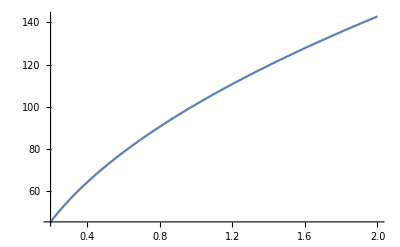

```mathematica
Plot[ maxLengthNoLoadsDimensional[200., h, 8, 9.8], {h, 0.2, 2}]
```

```mathematica
Solve[{
σY == ((w L^2)/8 + (P L)/4)(h/2)/((A h^2)/4),
w == γ g ρWater A
}, {A, L}] // FullSimplify
```

{{A→w/(g γ ρWater),L→-(g P γ ρWater+√(g γ ρWater (g P^2 γ ρWater+4 h w^2 σY)))/(g w γ ρWater)},{A→w/(g γ ρWater),L→(-g P γ ρWater+√(g γ ρWater (g P^2 γ ρWater+4 h w^2 σY)))/(g w γ ρWater)}}

```mathematica
P -> Phat g γ ρWater L
```

```mathematica
(γ g ρWater A L /.{P -> (Phat g γ ρWater L)} /. {A->w/(g γ ρWater),L->1/(g w γ ρWater)(-g (Phat g γ ρWater L) γ ρWater+√(g γ ρWater (g (Phat g γ ρWater L)^2 γ ρWater+4 h w^2 σY)))}) // PowerExpand// FullSimplify[#, Phat>0]& // PowerExpand // Cancel // FullSimplify
```

-g L Phat γ ρWater+(√(g^3 L^2 Phat^2 γ^3 ρWater^3+4 h w^2 σY))/(√g √γ √ρWater)

```mathematica
-g L Phat γ ρWater+(√(g^3 L^2 Phat^2 γ^3 ρWater^3+4 h w^2 σY))/(√g √γ √ρWater) /. {Phat -> Phh /(g L  γ ρWater), w ->  wh √(g γ ρWater)}// Factor// PowerExpand // FullSimplify
```

-Phh+√(Phh^2+4 h wh^2 σY)

```mathematica
P/(g L γ ρWater)^2 (√(1 + 4 h σY (g^3 L^4 w^2 γ^3 ρWater^3)/P^2) - 1)
```

P/(g^2 L^2 γ^2 ρWater^2)

```mathematica
FullSimplify[(w/(P/(g L γ ρWater)^2 √(g γ ρWater)))^2]
```

(g^3 L^4 w^2 γ^3 ρWater^3)/P^2

```mathematica
γ g ρWater (-(2 L P)/(g L^2 γ ρWater-4 h σY))L // FullSimplify // Expand
```

-(2 g L^2 P γ ρWater)/(g L^2 γ ρWater-4 h σY)

```mathematica
2/(4 (h σY)/(g L^2  γ ρWater) - 1)P
```

```mathematica
w/(g γ ρWater) * (-g P γ ρWater+√(g γ ρWater (g P^2 γ ρWater+4 h w^2 σY)))/(g w γ ρWater) // FullSimplify
```

```mathematica
(-g P γ ρWater+√(g γ ρWater (g P^2 γ ρWater+4 h w^2 σY)))/(g^2 γ^2 ρWater^2) // PowerExpand // Cancel // FullSimplify
```

```mathematica
-P/(g γ ρWater)+(√(g P^2 γ ρWater+4 h w^2 σY))/(g^(3/2) γ^(3/2) ρWater^(3/2)) /. {g -> gγρ / (γ ρWater)} // PowerExpand//Cancel // FullSimplify
```

```mathematica
-P/gγρ+(√(gγρ P^2+4 h w^2 σY))/gγρ^(3/2) /. {P -> Phat * gγρ} // PowerExpand//Cancel // FullSimplify[#, Assumptions -> {P>0}]&
```

```mathematica
-Phat+(√(gγρ^3 Phat^2+4 h (γ g ρWater A)^2 σY))/gγρ^(3/2)
```

```mathematica
γ g ρWater A L //.{IinertiaMax-> (A h^2)/4,L->(-h^2 P+√(h^4 P^2+64 g h IinertiaMax^2 γ ρWater σY))/(4 g IinertiaMax γ ρWater),A->(4 IinertiaMax)/h^2,w->(4 g IinertiaMax γ ρWater)/h^2}
```

ReplaceRepeated::rrlim: Exiting after A g L γ ρWater scanned 65536 times.

(-h^2 P+√(h^4 P^2+4 A^2 g h^5 γ ρWater σY))/h^2

### Solution

```mathematica
soln = Solve[{
σY == ((w L^2)/8 + (P L)/4)(h/2)/((A h^2)/4),
w == γ g ρWater A,
L0max == 2 √((σY h)/(γ ρWater g))
}, {A, w, σY}] // FullSimplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{A→-(2 L P)/(g L^2 γ ρWater-g L0max^2 γ ρWater),w→-(2 L P)/(L^2-L0max^2),σY→(g L0max^2 γ ρWater)/(4 h)}}

```mathematica
((w L)/P/. soln /. {L0max -> Lhat L} // FullSimplify)
```

{2/(-1+Lhat^2)}

#### Explore

```mathematica
WminOverPDimensional[30, 200., 1., 8]
```

0.193607

```mathematica
WminOverPDimensional[30, 200,1., 8,9.81 ]* Quantity[2 * 1000, "Kilograms"]
```

387.215 kg

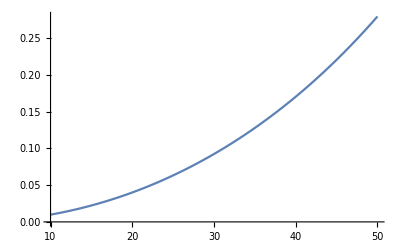

```mathematica
Plot[WminOverPDimensional[L, 200,2, 8], {L, 10, 50}]
```